```mathematica
<<BISfit`;
<<Data`;
Needs["PlotLegends`"];
```

PlotLegend::shdw: Symbol PlotLegend appears in multiple contexts PlotLegends`Global`; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear will be suppressed during this calculation.

```mathematica
(* check Cole fitted data, 
WARNING: old data used*)
```

```mathematica
data=ColeData[];
(*fd=Filterd[data[[9]]];*)
(*fdata=Map[Filterd,data];*)
(*fdata[[All,All,1]];*)
```

{32,8,4}

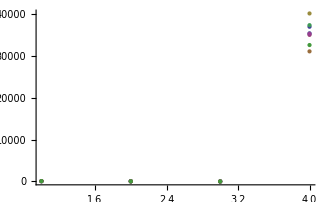

```mathematica
Dimensions[data]
ListPlot[data[[1,All,All]]]
```

```mathematica
(*Min[fdata[[All,All,1]]]*)
```

```mathematica
(*first filter bad data*)
```

```mathematica
fdata=Map[Filterd,data];
Dimensions[fdata]
```

```mathematica
lfd=Map[Length,fdata]
(*fdata//MatrixForm;*)
fdata[[2,3]]
```

{2,8,8,8,8,3,8,7,8,2,7,5,2,8,7,7,6,8,8,8,8,8,8,7,6,8,6,8,7,7,8,7}

{93.1295,43.8891,0.770356,33011.8}

```mathematica
(* Euclidean distance distribution*)
```

```mathematica
ddiff=Flatten[Reap[For[i=1,i≤Length[fdata]-1,i++,
For[j=i+1,j≤Length[fdata],j++,
Sow[Flatten[Outer[EuclideanDistance,fdata[[i]],fdata[[j]],1]]]
]]
][[2,1]]];

dsame=Reap[For[i=1,i≤Length[fdata],i++,
For[j=1,j≤Length[fdata[[i]]]-1,j++,
For[k=j+1,k<=Length[fdata[[i]]],k++,
Sow[EuclideanDistance[fdata[[i]][[j]],fdata[[i]][[k]]]];
(*Sow[-Mdistance[fdata[[i]][[j]],fdata[[i]][[k]]]];*)
]]]
][[2,1]];
```

```mathematica
{ns,nd}={Length[dsame],Length[ddiff]}
```

{677,22543}

```mathematica
Min[dsame]
Max[dsame]
Min[ddiff]
Max[ddiff]
```

1.58041

69791.2

5.29947

96547.8

```mathematica
hs=Histogram[dsame,{0,70000,200},"Probability",ColorFunction->Function[{x},Black]];
hd=Histogram[ddiff,{0,70000,400},"Probability",ChartStyle->Opacity[0.5](*,ColorFunction->Function[{x},Black]*)];
```

```mathematica
Histogram[{dsame,ddiff},{0,50000,300},"Probability",ChartLayout->"Overlapped"]
```

-Graphics-

```mathematica
Show[hs,hd,PlotRange->{{0,20000},{0,0.2}},FrameLabel->{"Frequency (Hz)","Resistance (Ω)"}]
```

-Graphics-

```mathematica
dds=BinCounts[dsame,{0,70000,200}]/ns;
ddd=BinCounts[ddiff,{0,100000,200}]/nd;
```

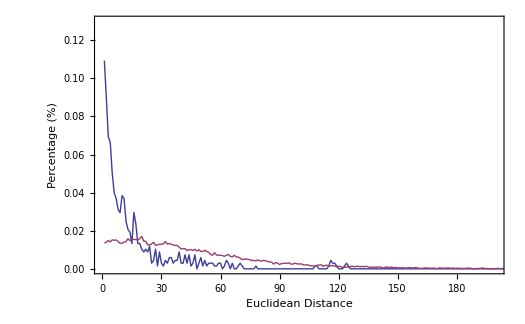

```mathematica
ListPlot[{dds,ddd},Joined->True,PlotRange->{{0,200},{0,0.13}},Frame->True,FrameLabel->{"Euclidean Distance","Percentage (%)"}]
```

```mathematica
(* now try normalize the data first*)
```

```mathematica
ffdata=Flatten[fdata,1];
Dimensions[ffdata]
sdata=Standardize[ffdata];
nsdata=Reap[For[i=1;td=sdata,i≤Length[lfd],i++,
Sow[Take[td,lfd[[i]]]];
td=Drop[td,lfd[[i]]];
]][[2,1]];

Dimensions[nsdata]
```

{216,4}

```mathematica
ddiff=Flatten[Reap[For[i=1,i≤Length[nsdata]-1,i++,
For[j=i+1,j≤Length[nsdata],j++,
Sow[Flatten[Outer[EuclideanDistance,nsdata[[i]],nsdata[[j]],1]]]
]]
][[2,1]]];

dsame=Reap[For[i=1,i≤Length[nsdata],i++,
For[j=1,j≤Length[nsdata[[i]]]-1,j++,
For[k=j+1,k<=Length[nsdata[[i]]],k++,
Sow[EuclideanDistance[nsdata[[i]][[j]],nsdata[[i]][[k]]]];
(*Sow[-Mdistance[fdata[[i]][[j]],fdata[[i]][[k]]]];*)
]]]
][[2,1]];
```

```mathematica
Length[dsame]
```

677

```mathematica
Histogram[{dsame,ddiff},{0,12,0.1},"Probability",ChartLayout->"Overlapped"];
```

```mathematica
dds=BinCounts[dsame,{0,12,0.15}]/ns;
ddd=BinCounts[ddiff,{0,12,0.15}]/nd;
```

```mathematica
ListPlot[{dds,ddd},Joined->True,PlotRange->{{0,60},{0,0.21}},Frame->True,FrameLabel->{"Euclidean Distance","Percentage (%)"},PlotStyle->{{Dashed,Thickness[0.002]},{Dotted,Thickness[0.003]}},PlotLegend->{"Innerclass", "Interclass"},LegendShadow->None]
```